## Information and copyright

Simulation code associated with “Projecting the transmission dynamics of SARS-CoV-2 through the post-pandemic period”, 
by S.M. Kissler*, C. Tedijanto*, E. Goldstein, Y.H. Grad, and M. Lipsitch
* denotes equal contribution
Correspondence: skissler@hsph.harvard.edu

Last modified: 22 March 2020

    This program is free software: you can redistribute it and/or modify
    it under the terms of the GNU General Public License as published by
    the Free Software Foundation, either version 3 of the License, or
    (at your option) any later version.

    This program is distributed in the hope that it will be useful,
    but WITHOUT ANY WARRANTY; without even the implied warranty of
    MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the
    GNU General Public License for more details.

    You should have received a copy of the GNU General Public License
    along with this program.  If not, see <https://www.gnu.org/licenses/>.

# Three-strain model

## Define forcing functions:

```mathematica
(*Seasonality function*)
betaval[t_,amplitude_,baseline_,phival_,gammaval_]:=gammaval*(amplitude/2*Cos[2*Pi*(t-phival)/52]+(amplitude/2+baseline))

(*Function for simulating importation of strain 1*)
p1[t_,kappaval_,importtime1_,importlength_]:=If[t>importtime1&& t≤(importtime1+importlength),kappaval,0]

(*Function for simulating importation of strain 2*)
p2[t_,kappaval_,importtime2_,importlength_]:=If[t>importtime2&& t≤(importtime2+importlength),kappaval,0]

(*Function for simulating importation of strain 3*)
p3[t_,kappaval_,importtime3_,importlength_]:=If[t>importtime3&& t≤(importtime3+importlength),kappaval,0]
```

## Define model functions:

```mathematica
S1S2S3c1[t]:=betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2S3[t]+p1[t,kappaval,importtime1,importlength]*S1S2S3[t]

S1S2S3c2[t]:=betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2S3[t]+p2[t,kappaval,importtime2,importlength]*S1S2S3[t]

S1S2S3c3[t]:=betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1S2S3[t]+p3[t,kappaval,importtime3,importlength]*S1S2S3[t]

S1S2E3c1[t]:=(1-chi31val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2E3[t]+(1-chi31val)*p1[t,kappaval,importtime1,importlength]*S1S2E3[t]

S1S2E3c2[t]:=(1-chi32val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2E3[t]+(1-chi32val)*p2[t,kappaval,importtime2,importlength]*S1S2E3[t]

S1S2E3c3[t]:=nuval*S1S2E3[t]

S1S2I3c1[t]:=(1-chi31val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2I3[t]+(1-chi31val)*p1[t,kappaval,importtime1,importlength]*S1S2I3[t]

S1S2I3c2[t]:=(1-chi32val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2I3[t]+(1-chi32val)*p2[t,kappaval,importtime2,importlength]*S1S2I3[t]

S1S2I3c3[t]:=gammaval*S1S2I3[t]

S1S2R3c1[t]:=(1-chi31val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1S2R3[t]+(1-chi31val)*p1[t,kappaval,importtime1,importlength]*S1S2R3[t]

S1S2R3c2[t]:=(1-chi32val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*S1S2R3[t]+(1-chi32val)*p2[t,kappaval,importtime2,importlength]*S1S2R3[t]

S1S2R3c3[t]:=sigma3val*S1S2R3[t]

S1E2S3c1[t]:=(1-chi21val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2S3[t]+(1-chi21val)*p1[t,kappaval,importtime1,importlength]*S1E2S3[t]

S1E2S3c2[t]:=nuval*S1E2S3[t]

S1E2S3c3[t]:=(1-chi23val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1E2S3[t]+(1-chi23val)*p3[t,kappaval,importtime3,importlength]*S1E2S3[t]

S1E2E3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2E3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1E2E3[t]

S1E2E3c2[t]:=nuval*S1E2E3[t]

S1E2E3c3[t]:=nuval*S1E2E3[t]

S1E2I3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2I3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1E2I3[t]

S1E2I3c2[t]:=nuval*S1E2I3[t]

S1E2I3c3[t]:=gammaval*S1E2I3[t]

S1E2R3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1E2R3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1E2R3[t]

S1E2R3c2[t]:=nuval*S1E2R3[t]

S1E2R3c3[t]:=sigma3val*S1E2R3[t]

S1I2S3c1[t]:=(1-chi21val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2S3[t]+(1-chi21val)*p1[t,kappaval,importtime1,importlength]*S1I2S3[t]

S1I2S3c2[t]:=gammaval*S1I2S3[t]

S1I2S3c3[t]:=(1-chi23val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1I2S3[t]+(1-chi23val)*p3[t,kappaval,importtime3,importlength]*S1I2S3[t]

S1I2E3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2E3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1I2E3[t]

S1I2E3c2[t]:=gammaval*S1I2E3[t]

S1I2E3c3[t]:=nuval*S1I2E3[t]

S1I2I3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2I3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1I2I3[t]

S1I2I3c2[t]:=gammaval*S1I2I3[t]

S1I2I3c3[t]:=gammaval*S1I2I3[t]

S1I2R3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1I2R3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1I2R3[t]

S1I2R3c2[t]:=gammaval*S1I2R3[t]

S1I2R3c3[t]:=sigma3val*S1I2R3[t]

S1R2S3c1[t]:=(1-chi21val)*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2S3[t]+(1-chi21val)*p1[t,kappaval,importtime1,importlength]*S1R2S3[t]

S1R2S3c2[t]:=sigma2val*S1R2S3[t]

S1R2S3c3[t]:=(1-chi23val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*S1R2S3[t]+(1-chi23val)*p3[t,kappaval,importtime3,importlength]*S1R2S3[t]

S1R2E3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2E3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1R2E3[t]

S1R2E3c2[t]:=sigma2val*S1R2E3[t]

S1R2E3c3[t]:=nuval*S1R2E3[t]

S1R2I3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2I3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1R2I3[t]

S1R2I3c2[t]:=sigma2val*S1R2I3[t]

S1R2I3c3[t]:=gammaval*S1R2I3[t]

S1R2R3c1[t]:=(1-Max[chi21val,chi31val])*betaval[t,amplitude,baseline,phival,gammaval]*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])*S1R2R3[t]+(1-Max[chi21val,chi31val])*p1[t,kappaval,importtime1,importlength]*S1R2R3[t]

S1R2R3c2[t]:=sigma2val*S1R2R3[t]

S1R2R3c3[t]:=sigma3val*S1R2R3[t]

E1S2S3c1[t]:=nuval*E1S2S3[t]

E1S2S3c2[t]:=(1-chi12val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2S3[t]+(1-chi12val)*p2[t,kappaval,importtime2,importlength]*E1S2S3[t]

E1S2S3c3[t]:=(1-chi13val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1S2S3[t]+(1-chi13val)*p3[t,kappaval,importtime3,importlength]*E1S2S3[t]

E1S2E3c1[t]:=nuval*E1S2E3[t]

E1S2E3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2E3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*E1S2E3[t]

E1S2E3c3[t]:=nuval*E1S2E3[t]

E1S2I3c1[t]:=nuval*E1S2I3[t]

E1S2I3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2I3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*E1S2I3[t]

E1S2I3c3[t]:=gammaval*E1S2I3[t]

E1S2R3c1[t]:=nuval*E1S2R3[t]

E1S2R3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*E1S2R3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*E1S2R3[t]

E1S2R3c3[t]:=sigma3val*E1S2R3[t]

E1E2S3c1[t]:=nuval*E1E2S3[t]

E1E2S3c2[t]:=nuval*E1E2S3[t]

E1E2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1E2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*E1E2S3[t]

E1E2E3c1[t]:=nuval*E1E2E3[t]

E1E2E3c2[t]:=nuval*E1E2E3[t]

E1E2E3c3[t]:=nuval*E1E2E3[t]

E1E2I3c1[t]:=nuval*E1E2I3[t]

E1E2I3c2[t]:=nuval*E1E2I3[t]

E1E2I3c3[t]:=gammaval*E1E2I3[t]

E1E2R3c1[t]:=nuval*E1E2R3[t]

E1E2R3c2[t]:=nuval*E1E2R3[t]

E1E2R3c3[t]:=sigma3val*E1E2R3[t]

E1I2S3c1[t]:=nuval*E1I2S3[t]

E1I2S3c2[t]:=gammaval*E1I2S3[t]

E1I2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1I2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*E1I2S3[t]

E1I2E3c1[t]:=nuval*E1I2E3[t]

E1I2E3c2[t]:=gammaval*E1I2E3[t]

E1I2E3c3[t]:=nuval*E1I2E3[t]

E1I2I3c1[t]:=nuval*E1I2I3[t]

E1I2I3c2[t]:=gammaval*E1I2I3[t]

E1I2I3c3[t]:=gammaval*E1I2I3[t]

E1I2R3c1[t]:=nuval*E1I2R3[t]

E1I2R3c2[t]:=gammaval*E1I2R3[t]

E1I2R3c3[t]:=sigma3val*E1I2R3[t]

E1R2S3c1[t]:=nuval*E1R2S3[t]

E1R2S3c2[t]:=sigma2val*E1R2S3[t]

E1R2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*E1R2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*E1R2S3[t]

E1R2E3c1[t]:=nuval*E1R2E3[t]

E1R2E3c2[t]:=sigma2val*E1R2E3[t]

E1R2E3c3[t]:=nuval*E1R2E3[t]

E1R2I3c1[t]:=nuval*E1R2I3[t]

E1R2I3c2[t]:=sigma2val*E1R2I3[t]

E1R2I3c3[t]:=gammaval*E1R2I3[t]

E1R2R3c1[t]:=nuval*E1R2R3[t]

E1R2R3c2[t]:=sigma2val*E1R2R3[t]

E1R2R3c3[t]:=sigma3val*E1R2R3[t]

I1S2S3c1[t]:=gammaval*I1S2S3[t]

I1S2S3c2[t]:=(1-chi12val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2S3[t]+(1-chi12val)*p2[t,kappaval,importtime2,importlength]*I1S2S3[t]

I1S2S3c3[t]:=(1-chi13val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1S2S3[t]+(1-chi13val)*p3[t,kappaval,importtime3,importlength]*I1S2S3[t]

I1S2E3c1[t]:=gammaval*I1S2E3[t]

I1S2E3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2E3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*I1S2E3[t]

I1S2E3c3[t]:=nuval*I1S2E3[t]

I1S2I3c1[t]:=gammaval*I1S2I3[t]

I1S2I3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2I3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*I1S2I3[t]

I1S2I3c3[t]:=gammaval*I1S2I3[t]

I1S2R3c1[t]:=gammaval*I1S2R3[t]

I1S2R3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*I1S2R3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*I1S2R3[t]

I1S2R3c3[t]:=sigma3val*I1S2R3[t]

I1E2S3c1[t]:=gammaval*I1E2S3[t]

I1E2S3c2[t]:=nuval*I1E2S3[t]

I1E2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1E2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*I1E2S3[t]

I1E2E3c1[t]:=gammaval*I1E2E3[t]

I1E2E3c2[t]:=nuval*I1E2E3[t]

I1E2E3c3[t]:=nuval*I1E2E3[t]

I1E2I3c1[t]:=gammaval*I1E2I3[t]

I1E2I3c2[t]:=nuval*I1E2I3[t]

I1E2I3c3[t]:=gammaval*I1E2I3[t]

I1E2R3c1[t]:=gammaval*I1E2R3[t]

I1E2R3c2[t]:=nuval*I1E2R3[t]

I1E2R3c3[t]:=sigma3val*I1E2R3[t]

I1I2S3c1[t]:=gammaval*I1I2S3[t]

I1I2S3c2[t]:=gammaval*I1I2S3[t]

I1I2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1I2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*I1I2S3[t]

I1I2E3c1[t]:=gammaval*I1I2E3[t]

I1I2E3c2[t]:=gammaval*I1I2E3[t]

I1I2E3c3[t]:=nuval*I1I2E3[t]

I1I2I3c1[t]:=gammaval*I1I2I3[t]

I1I2I3c2[t]:=gammaval*I1I2I3[t]

I1I2I3c3[t]:=gammaval*I1I2I3[t]

I1I2R3c1[t]:=gammaval*I1I2R3[t]

I1I2R3c2[t]:=gammaval*I1I2R3[t]

I1I2R3c3[t]:=sigma3val*I1I2R3[t]

I1R2S3c1[t]:=gammaval*I1R2S3[t]

I1R2S3c2[t]:=sigma2val*I1R2S3[t]

I1R2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*I1R2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*I1R2S3[t]

I1R2E3c1[t]:=gammaval*I1R2E3[t]

I1R2E3c2[t]:=sigma2val*I1R2E3[t]

I1R2E3c3[t]:=nuval*I1R2E3[t]

I1R2I3c1[t]:=gammaval*I1R2I3[t]

I1R2I3c2[t]:=sigma2val*I1R2I3[t]

I1R2I3c3[t]:=gammaval*I1R2I3[t]

I1R2R3c1[t]:=gammaval*I1R2R3[t]

I1R2R3c2[t]:=sigma2val*I1R2R3[t]

I1R2R3c3[t]:=sigma3val*I1R2R3[t]

R1S2S3c1[t]:=sigma1val*R1S2S3[t]

R1S2S3c2[t]:=(1-chi12val)*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2S3[t]+(1-chi12val)*p2[t,kappaval,importtime2,importlength]*R1S2S3[t]

R1S2S3c3[t]:=(1-chi13val)*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1S2S3[t]+(1-chi13val)*p3[t,kappaval,importtime3,importlength]*R1S2S3[t]

R1S2E3c1[t]:=sigma1val*R1S2E3[t]

R1S2E3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2E3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*R1S2E3[t]

R1S2E3c3[t]:=nuval*R1S2E3[t]

R1S2I3c1[t]:=sigma1val*R1S2I3[t]

R1S2I3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2I3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*R1S2I3[t]

R1S2I3c3[t]:=gammaval*R1S2I3[t]

R1S2R3c1[t]:=sigma1val*R1S2R3[t]

R1S2R3c2[t]:=(1-Max[chi12val,chi32val])*betaval[t,amplitude,baseline,phival,gammaval]*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])*R1S2R3[t]+(1-Max[chi12val,chi32val])*p2[t,kappaval,importtime2,importlength]*R1S2R3[t]

R1S2R3c3[t]:=sigma3val*R1S2R3[t]

R1E2S3c1[t]:=sigma1val*R1E2S3[t]

R1E2S3c2[t]:=nuval*R1E2S3[t]

R1E2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1E2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*R1E2S3[t]

R1E2E3c1[t]:=sigma1val*R1E2E3[t]

R1E2E3c2[t]:=nuval*R1E2E3[t]

R1E2E3c3[t]:=nuval*R1E2E3[t]

R1E2I3c1[t]:=sigma1val*R1E2I3[t]

R1E2I3c2[t]:=nuval*R1E2I3[t]

R1E2I3c3[t]:=gammaval*R1E2I3[t]

R1E2R3c1[t]:=sigma1val*R1E2R3[t]

R1E2R3c2[t]:=nuval*R1E2R3[t]

R1E2R3c3[t]:=sigma3val*R1E2R3[t]

R1I2S3c1[t]:=sigma1val*R1I2S3[t]

R1I2S3c2[t]:=gammaval*R1I2S3[t]

R1I2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1I2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*R1I2S3[t]

R1I2E3c1[t]:=sigma1val*R1I2E3[t]

R1I2E3c2[t]:=gammaval*R1I2E3[t]

R1I2E3c3[t]:=nuval*R1I2E3[t]

R1I2I3c1[t]:=sigma1val*R1I2I3[t]

R1I2I3c2[t]:=gammaval*R1I2I3[t]

R1I2I3c3[t]:=gammaval*R1I2I3[t]

R1I2R3c1[t]:=sigma1val*R1I2R3[t]

R1I2R3c2[t]:=gammaval*R1I2R3[t]

R1I2R3c3[t]:=sigma3val*R1I2R3[t]

R1R2S3c1[t]:=sigma1val*R1R2S3[t]

R1R2S3c2[t]:=sigma2val*R1R2S3[t]

R1R2S3c3[t]:=(1-Max[chi13val,chi23val])*betaval[t,f*amplitude,baseline+(1-f)*amplitude,phival,gammaval]*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])*R1R2S3[t]+(1-Max[chi13val,chi23val])*p3[t,kappaval,importtime3,importlength]*R1R2S3[t]

R1R2E3c1[t]:=sigma1val*R1R2E3[t]

R1R2E3c2[t]:=sigma2val*R1R2E3[t]

R1R2E3c3[t]:=nuval*R1R2E3[t]

R1R2I3c1[t]:=sigma1val*R1R2I3[t]

R1R2I3c2[t]:=sigma2val*R1R2I3[t]

R1R2I3c3[t]:=gammaval*R1R2I3[t]

R1R2R3c1[t]:=sigma1val*R1R2R3[t]

R1R2R3c2[t]:=sigma2val*R1R2R3[t]

R1R2R3c3[t]:=sigma3val*R1R2R3[t]
```

## Define model solver:

```mathematica
runmodel3strain[] := NDSolve[
{S1S2S3'[t]==-S1S2S3c1[t]-S1S2S3c2[t]-S1S2S3c3[t]+R1S2S3c1[t]+S1R2S3c2[t]+S1S2R3c3[t]-muval*S1S2S3[t]+muval,S1S2E3'[t]==-S1S2E3c1[t]-S1S2E3c2[t]-S1S2E3c3[t]+R1S2E3c1[t]+S1R2E3c2[t]+S1S2S3c3[t]-muval*S1S2E3[t],S1S2I3'[t]==-S1S2I3c1[t]-S1S2I3c2[t]-S1S2I3c3[t]+R1S2I3c1[t]+S1R2I3c2[t]+S1S2E3c3[t]-muval*S1S2I3[t],S1S2R3'[t]==-S1S2R3c1[t]-S1S2R3c2[t]-S1S2R3c3[t]+R1S2R3c1[t]+S1R2R3c2[t]+S1S2I3c3[t]-muval*S1S2R3[t],S1E2S3'[t]==-S1E2S3c1[t]-S1E2S3c2[t]-S1E2S3c3[t]+R1E2S3c1[t]+S1S2S3c2[t]+S1E2R3c3[t]-muval*S1E2S3[t],S1E2E3'[t]==-S1E2E3c1[t]-S1E2E3c2[t]-S1E2E3c3[t]+R1E2E3c1[t]+S1S2E3c2[t]+S1E2S3c3[t]-muval*S1E2E3[t],S1E2I3'[t]==-S1E2I3c1[t]-S1E2I3c2[t]-S1E2I3c3[t]+R1E2I3c1[t]+S1S2I3c2[t]+S1E2E3c3[t]-muval*S1E2I3[t],S1E2R3'[t]==-S1E2R3c1[t]-S1E2R3c2[t]-S1E2R3c3[t]+R1E2R3c1[t]+S1S2R3c2[t]+S1E2I3c3[t]-muval*S1E2R3[t],S1I2S3'[t]==-S1I2S3c1[t]-S1I2S3c2[t]-S1I2S3c3[t]+R1I2S3c1[t]+S1E2S3c2[t]+S1I2R3c3[t]-muval*S1I2S3[t],S1I2E3'[t]==-S1I2E3c1[t]-S1I2E3c2[t]-S1I2E3c3[t]+R1I2E3c1[t]+S1E2E3c2[t]+S1I2S3c3[t]-muval*S1I2E3[t],S1I2I3'[t]==-S1I2I3c1[t]-S1I2I3c2[t]-S1I2I3c3[t]+R1I2I3c1[t]+S1E2I3c2[t]+S1I2E3c3[t]-muval*S1I2I3[t],S1I2R3'[t]==-S1I2R3c1[t]-S1I2R3c2[t]-S1I2R3c3[t]+R1I2R3c1[t]+S1E2R3c2[t]+S1I2I3c3[t]-muval*S1I2R3[t],S1R2S3'[t]==-S1R2S3c1[t]-S1R2S3c2[t]-S1R2S3c3[t]+R1R2S3c1[t]+S1I2S3c2[t]+S1R2R3c3[t]-muval*S1R2S3[t],S1R2E3'[t]==-S1R2E3c1[t]-S1R2E3c2[t]-S1R2E3c3[t]+R1R2E3c1[t]+S1I2E3c2[t]+S1R2S3c3[t]-muval*S1R2E3[t],S1R2I3'[t]==-S1R2I3c1[t]-S1R2I3c2[t]-S1R2I3c3[t]+R1R2I3c1[t]+S1I2I3c2[t]+S1R2E3c3[t]-muval*S1R2I3[t],S1R2R3'[t]==-S1R2R3c1[t]-S1R2R3c2[t]-S1R2R3c3[t]+R1R2R3c1[t]+S1I2R3c2[t]+S1R2I3c3[t]-muval*S1R2R3[t],E1S2S3'[t]==-E1S2S3c1[t]-E1S2S3c2[t]-E1S2S3c3[t]+S1S2S3c1[t]+E1R2S3c2[t]+E1S2R3c3[t]-muval*E1S2S3[t],E1S2E3'[t]==-E1S2E3c1[t]-E1S2E3c2[t]-E1S2E3c3[t]+S1S2E3c1[t]+E1R2E3c2[t]+E1S2S3c3[t]-muval*E1S2E3[t],E1S2I3'[t]==-E1S2I3c1[t]-E1S2I3c2[t]-E1S2I3c3[t]+S1S2I3c1[t]+E1R2I3c2[t]+E1S2E3c3[t]-muval*E1S2I3[t],E1S2R3'[t]==-E1S2R3c1[t]-E1S2R3c2[t]-E1S2R3c3[t]+S1S2R3c1[t]+E1R2R3c2[t]+E1S2I3c3[t]-muval*E1S2R3[t],E1E2S3'[t]==-E1E2S3c1[t]-E1E2S3c2[t]-E1E2S3c3[t]+S1E2S3c1[t]+E1S2S3c2[t]+E1E2R3c3[t]-muval*E1E2S3[t],E1E2E3'[t]==-E1E2E3c1[t]-E1E2E3c2[t]-E1E2E3c3[t]+S1E2E3c1[t]+E1S2E3c2[t]+E1E2S3c3[t]-muval*E1E2E3[t],E1E2I3'[t]==-E1E2I3c1[t]-E1E2I3c2[t]-E1E2I3c3[t]+S1E2I3c1[t]+E1S2I3c2[t]+E1E2E3c3[t]-muval*E1E2I3[t],E1E2R3'[t]==-E1E2R3c1[t]-E1E2R3c2[t]-E1E2R3c3[t]+S1E2R3c1[t]+E1S2R3c2[t]+E1E2I3c3[t]-muval*E1E2R3[t],E1I2S3'[t]==-E1I2S3c1[t]-E1I2S3c2[t]-E1I2S3c3[t]+S1I2S3c1[t]+E1E2S3c2[t]+E1I2R3c3[t]-muval*E1I2S3[t],E1I2E3'[t]==-E1I2E3c1[t]-E1I2E3c2[t]-E1I2E3c3[t]+S1I2E3c1[t]+E1E2E3c2[t]+E1I2S3c3[t]-muval*E1I2E3[t],E1I2I3'[t]==-E1I2I3c1[t]-E1I2I3c2[t]-E1I2I3c3[t]+S1I2I3c1[t]+E1E2I3c2[t]+E1I2E3c3[t]-muval*E1I2I3[t],E1I2R3'[t]==-E1I2R3c1[t]-E1I2R3c2[t]-E1I2R3c3[t]+S1I2R3c1[t]+E1E2R3c2[t]+E1I2I3c3[t]-muval*E1I2R3[t],E1R2S3'[t]==-E1R2S3c1[t]-E1R2S3c2[t]-E1R2S3c3[t]+S1R2S3c1[t]+E1I2S3c2[t]+E1R2R3c3[t]-muval*E1R2S3[t],E1R2E3'[t]==-E1R2E3c1[t]-E1R2E3c2[t]-E1R2E3c3[t]+S1R2E3c1[t]+E1I2E3c2[t]+E1R2S3c3[t]-muval*E1R2E3[t],E1R2I3'[t]==-E1R2I3c1[t]-E1R2I3c2[t]-E1R2I3c3[t]+S1R2I3c1[t]+E1I2I3c2[t]+E1R2E3c3[t]-muval*E1R2I3[t],E1R2R3'[t]==-E1R2R3c1[t]-E1R2R3c2[t]-E1R2R3c3[t]+S1R2R3c1[t]+E1I2R3c2[t]+E1R2I3c3[t]-muval*E1R2R3[t],I1S2S3'[t]==-I1S2S3c1[t]-I1S2S3c2[t]-I1S2S3c3[t]+E1S2S3c1[t]+I1R2S3c2[t]+I1S2R3c3[t]-muval*I1S2S3[t],I1S2E3'[t]==-I1S2E3c1[t]-I1S2E3c2[t]-I1S2E3c3[t]+E1S2E3c1[t]+I1R2E3c2[t]+I1S2S3c3[t]-muval*I1S2E3[t],I1S2I3'[t]==-I1S2I3c1[t]-I1S2I3c2[t]-I1S2I3c3[t]+E1S2I3c1[t]+I1R2I3c2[t]+I1S2E3c3[t]-muval*I1S2I3[t],I1S2R3'[t]==-I1S2R3c1[t]-I1S2R3c2[t]-I1S2R3c3[t]+E1S2R3c1[t]+I1R2R3c2[t]+I1S2I3c3[t]-muval*I1S2R3[t],I1E2S3'[t]==-I1E2S3c1[t]-I1E2S3c2[t]-I1E2S3c3[t]+E1E2S3c1[t]+I1S2S3c2[t]+I1E2R3c3[t]-muval*I1E2S3[t],I1E2E3'[t]==-I1E2E3c1[t]-I1E2E3c2[t]-I1E2E3c3[t]+E1E2E3c1[t]+I1S2E3c2[t]+I1E2S3c3[t]-muval*I1E2E3[t],I1E2I3'[t]==-I1E2I3c1[t]-I1E2I3c2[t]-I1E2I3c3[t]+E1E2I3c1[t]+I1S2I3c2[t]+I1E2E3c3[t]-muval*I1E2I3[t],I1E2R3'[t]==-I1E2R3c1[t]-I1E2R3c2[t]-I1E2R3c3[t]+E1E2R3c1[t]+I1S2R3c2[t]+I1E2I3c3[t]-muval*I1E2R3[t],I1I2S3'[t]==-I1I2S3c1[t]-I1I2S3c2[t]-I1I2S3c3[t]+E1I2S3c1[t]+I1E2S3c2[t]+I1I2R3c3[t]-muval*I1I2S3[t],I1I2E3'[t]==-I1I2E3c1[t]-I1I2E3c2[t]-I1I2E3c3[t]+E1I2E3c1[t]+I1E2E3c2[t]+I1I2S3c3[t]-muval*I1I2E3[t],I1I2I3'[t]==-I1I2I3c1[t]-I1I2I3c2[t]-I1I2I3c3[t]+E1I2I3c1[t]+I1E2I3c2[t]+I1I2E3c3[t]-muval*I1I2I3[t],I1I2R3'[t]==-I1I2R3c1[t]-I1I2R3c2[t]-I1I2R3c3[t]+E1I2R3c1[t]+I1E2R3c2[t]+I1I2I3c3[t]-muval*I1I2R3[t],I1R2S3'[t]==-I1R2S3c1[t]-I1R2S3c2[t]-I1R2S3c3[t]+E1R2S3c1[t]+I1I2S3c2[t]+I1R2R3c3[t]-muval*I1R2S3[t],I1R2E3'[t]==-I1R2E3c1[t]-I1R2E3c2[t]-I1R2E3c3[t]+E1R2E3c1[t]+I1I2E3c2[t]+I1R2S3c3[t]-muval*I1R2E3[t],I1R2I3'[t]==-I1R2I3c1[t]-I1R2I3c2[t]-I1R2I3c3[t]+E1R2I3c1[t]+I1I2I3c2[t]+I1R2E3c3[t]-muval*I1R2I3[t],I1R2R3'[t]==-I1R2R3c1[t]-I1R2R3c2[t]-I1R2R3c3[t]+E1R2R3c1[t]+I1I2R3c2[t]+I1R2I3c3[t]-muval*I1R2R3[t],R1S2S3'[t]==-R1S2S3c1[t]-R1S2S3c2[t]-R1S2S3c3[t]+I1S2S3c1[t]+R1R2S3c2[t]+R1S2R3c3[t]-muval*R1S2S3[t],R1S2E3'[t]==-R1S2E3c1[t]-R1S2E3c2[t]-R1S2E3c3[t]+I1S2E3c1[t]+R1R2E3c2[t]+R1S2S3c3[t]-muval*R1S2E3[t],R1S2I3'[t]==-R1S2I3c1[t]-R1S2I3c2[t]-R1S2I3c3[t]+I1S2I3c1[t]+R1R2I3c2[t]+R1S2E3c3[t]-muval*R1S2I3[t],R1S2R3'[t]==-R1S2R3c1[t]-R1S2R3c2[t]-R1S2R3c3[t]+I1S2R3c1[t]+R1R2R3c2[t]+R1S2I3c3[t]-muval*R1S2R3[t],R1E2S3'[t]==-R1E2S3c1[t]-R1E2S3c2[t]-R1E2S3c3[t]+I1E2S3c1[t]+R1S2S3c2[t]+R1E2R3c3[t]-muval*R1E2S3[t],R1E2E3'[t]==-R1E2E3c1[t]-R1E2E3c2[t]-R1E2E3c3[t]+I1E2E3c1[t]+R1S2E3c2[t]+R1E2S3c3[t]-muval*R1E2E3[t],R1E2I3'[t]==-R1E2I3c1[t]-R1E2I3c2[t]-R1E2I3c3[t]+I1E2I3c1[t]+R1S2I3c2[t]+R1E2E3c3[t]-muval*R1E2I3[t],R1E2R3'[t]==-R1E2R3c1[t]-R1E2R3c2[t]-R1E2R3c3[t]+I1E2R3c1[t]+R1S2R3c2[t]+R1E2I3c3[t]-muval*R1E2R3[t],R1I2S3'[t]==-R1I2S3c1[t]-R1I2S3c2[t]-R1I2S3c3[t]+I1I2S3c1[t]+R1E2S3c2[t]+R1I2R3c3[t]-muval*R1I2S3[t],R1I2E3'[t]==-R1I2E3c1[t]-R1I2E3c2[t]-R1I2E3c3[t]+I1I2E3c1[t]+R1E2E3c2[t]+R1I2S3c3[t]-muval*R1I2E3[t],R1I2I3'[t]==-R1I2I3c1[t]-R1I2I3c2[t]-R1I2I3c3[t]+I1I2I3c1[t]+R1E2I3c2[t]+R1I2E3c3[t]-muval*R1I2I3[t],R1I2R3'[t]==-R1I2R3c1[t]-R1I2R3c2[t]-R1I2R3c3[t]+I1I2R3c1[t]+R1E2R3c2[t]+R1I2I3c3[t]-muval*R1I2R3[t],R1R2S3'[t]==-R1R2S3c1[t]-R1R2S3c2[t]-R1R2S3c3[t]+I1R2S3c1[t]+R1I2S3c2[t]+R1R2R3c3[t]-muval*R1R2S3[t],R1R2E3'[t]==-R1R2E3c1[t]-R1R2E3c2[t]-R1R2E3c3[t]+I1R2E3c1[t]+R1I2E3c2[t]+R1R2S3c3[t]-muval*R1R2E3[t],R1R2I3'[t]==-R1R2I3c1[t]-R1R2I3c2[t]-R1R2I3c3[t]+I1R2I3c1[t]+R1I2I3c2[t]+R1R2E3c3[t]-muval*R1R2I3[t],R1R2R3'[t]==-R1R2R3c1[t]-R1R2R3c2[t]-R1R2R3c3[t]+I1R2R3c1[t]+R1I2R3c2[t]+R1R2I3c3[t]-muval*R1R2R3[t],
cuminf'[t]==E1S2S3c1[t]+E1S2E3c1[t]+E1S2I3c1[t]+E1S2R3c1[t]+E1E2S3c1[t]+E1E2E3c1[t]+E1E2I3c1[t]+E1E2R3c1[t]+E1I2S3c1[t]+E1I2E3c1[t]+E1I2I3c1[t]+E1I2R3c1[t]+E1R2S3c1[t]+E1R2E3c1[t]+E1R2I3c1[t]+E1R2R3c1[t]+S1E2S3c2[t]+S1E2E3c2[t]+S1E2I3c2[t]+S1E2R3c2[t]+E1E2S3c2[t]+E1E2E3c2[t]+E1E2I3c2[t]+E1E2R3c2[t]+I1E2S3c2[t]+I1E2E3c2[t]+I1E2I3c2[t]+I1E2R3c2[t]+R1E2S3c2[t]+R1E2E3c2[t]+R1E2I3c2[t]+R1E2R3c2[t]+S1S2E3c3[t]+S1E2E3c3[t]+S1I2E3c3[t]+S1R2E3c3[t]+E1S2E3c3[t]+E1E2E3c3[t]+E1I2E3c3[t]+E1R2E3c3[t]+I1S2E3c3[t]+I1E2E3c3[t]+I1I2E3c3[t]+I1R2E3c3[t]+R1S2E3c3[t]+R1E2E3c3[t]+R1I2E3c3[t]+R1R2E3c3[t],
S1S2S3[0]==1,S1S2E3[0]==0,S1S2I3[0]==0,S1S2R3[0]==0,S1E2S3[0]==0,S1E2E3[0]==0,S1E2I3[0]==0,S1E2R3[0]==0,S1I2S3[0]==0,S1I2E3[0]==0,S1I2I3[0]==0,S1I2R3[0]==0,S1R2S3[0]==0,S1R2E3[0]==0,S1R2I3[0]==0,S1R2R3[0]==0,E1S2S3[0]==0,E1S2E3[0]==0,E1S2I3[0]==0,E1S2R3[0]==0,E1E2S3[0]==0,E1E2E3[0]==0,E1E2I3[0]==0,E1E2R3[0]==0,E1I2S3[0]==0,E1I2E3[0]==0,E1I2I3[0]==0,E1I2R3[0]==0,E1R2S3[0]==0,E1R2E3[0]==0,E1R2I3[0]==0,E1R2R3[0]==0,I1S2S3[0]==0,I1S2E3[0]==0,I1S2I3[0]==0,I1S2R3[0]==0,I1E2S3[0]==0,I1E2E3[0]==0,I1E2I3[0]==0,I1E2R3[0]==0,I1I2S3[0]==0,I1I2E3[0]==0,I1I2I3[0]==0,I1I2R3[0]==0,I1R2S3[0]==0,I1R2E3[0]==0,I1R2I3[0]==0,I1R2R3[0]==0,R1S2S3[0]==0,R1S2E3[0]==0,R1S2I3[0]==0,R1S2R3[0]==0,R1E2S3[0]==0,R1E2E3[0]==0,R1E2I3[0]==0,R1E2R3[0]==0,R1I2S3[0]==0,R1I2E3[0]==0,R1I2I3[0]==0,R1I2R3[0]==0,R1R2S3[0]==0,R1R2E3[0]==0,R1R2I3[0]==0,R1R2R3[0]==0, cuminf[0]==0},
{S1S2S3,S1S2E3,S1S2I3,S1S2R3,S1E2S3,S1E2E3,S1E2I3,S1E2R3,S1I2S3,S1I2E3,S1I2I3,S1I2R3,S1R2S3,S1R2E3,S1R2I3,S1R2R3,E1S2S3,E1S2E3,E1S2I3,E1S2R3,E1E2S3,E1E2E3,E1E2I3,E1E2R3,E1I2S3,E1I2E3,E1I2I3,E1I2R3,E1R2S3,E1R2E3,E1R2I3,E1R2R3,I1S2S3,I1S2E3,I1S2I3,I1S2R3,I1E2S3,I1E2E3,I1E2I3,I1E2R3,I1I2S3,I1I2E3,I1I2I3,I1I2R3,I1R2S3,I1R2E3,I1R2I3,I1R2R3,R1S2S3,R1S2E3,R1S2I3,R1S2R3,R1E2S3,R1E2E3,R1E2I3,R1E2R3,R1I2S3,R1I2E3,R1I2I3,R1I2R3,R1R2S3,R1R2E3,R1R2I3,R1R2R3, cuminf},
{t, 0, tmax}
];
```

## Set default parameter values:

```mathematica
sigma1val = 1/40; (*Waning immunity rate, strain 1, weeks; default 1/40*)
sigma2val = 1/38; (*Waning immunity rate, strain 1, weeks; default 1/40*)
sigma3val = 1/104; (*Waning immunity rate, strain 1, weeks; default 1/40*)
nuval = 1/(4.9/7);  (*Rate of progression to infection, weeks; default 1/1*)
gammaval = 1/(4.8/7); (*Rate of recovery, weeks; default 1/1*)
chi12val = 0.74; (*Cross immunity, strain 1 to 2*)
chi21val = 0.5; (*Cross immunity, strain 2 to 1*)
chi13val=0.0; (*Cross immunity, strain 1 to 2*)
chi31val=0.7; (*Cross immunity, strain 3 to 1*)
chi23val=0.0; (*Cross immunity, strain 2 to 3*)
chi32val=0.7; (*Cross immunity, strain 3 to 2*)
amplitude=0.66; (*Amplitude of seasonal R0*)
baseline=1.4; (*Baseline Ro value*)
phival=-3.8; (*Phase shift for seasonal R0 (weeks)*)
kappaval = 0.01; (*Boost from importations*)
importtime1 = 0; (*Importation time for strain 1, weeks*)
importtime2 = 52;  (*Importation time for strain 2, weeks*)
importtime3= 52*100(*52*24+12*);  (*Importation time for strain 3, weeks*)
importlength = 0.5; (*How long does an importation boost transmission, in weeks?*)
muval = 1/(80*52); (* birth rate, in weeks *) 
f = 1; (*Seasonality factor (1 = full seasonality, 0 = no seasonality so that R0 stays fixed at its maximal wintertime value*)
```

```mathematica
scalingfactor = 0.075; (*Conversion between prevalence and (% positive * % ILI) *)
```

```mathematica
tmax = 52*30; (*Simulation timespan, weeks*)
```

```mathematica
plotwindow = {52*20.5, 52*27.5}; (*Time span for plotting*)
plotrangemax = 0.8; (*Max plotting value *)
importbarchar = {Black, Thick}; (*For plotting the bar marking the importation time*)
yearbarchar = {Gray, Thin}; (*For marking years*)
fs = 18; (*Plot font size*)
imsz = 475; (*plot image size*)
ncovticks = {100*scalingfactor*#, ToString[N[1000*#]]}&/@N[FindDivisions[{0, 1/(100*scalingfactor)*plotrangemax},5]];
oc43char = {Blue,Thickness[0.008], Opacity[0.5]}; (*Plotting characteristics for HCoV-OC43*)
hku1char = {Red, Thickness[0.008], Opacity[0.5]};(*Plotting characteristics for HCoV-HKU1*)
ncovchar={Black, Thickness[0.008], Opacity[0.5]};(*Plotting characteristics for HCoV-SARS-CoV-2*)
totalchar={Black, Thickness[0.004], Opacity[0.5],Dashed};(*Plotting characteristics for the total prevalence curve*)
```

## Run some scenarios (Figure 3):

### 70/0 | 104 | w4:

#### Define parameter values:

```mathematica
chi31val=0.7;
chi32val = 0.7;
chi13val = 0;
chi23val = 0;
sigma3val = 1/104;
importtime3 = 52*22 + 4;
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

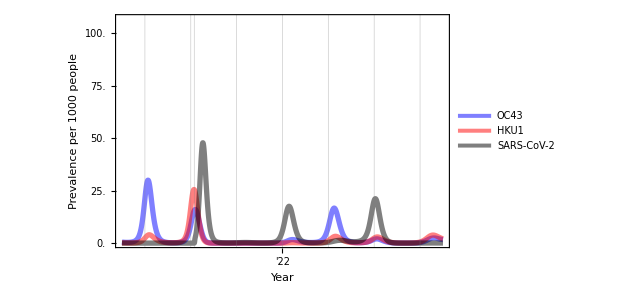

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3E.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3E.png",figinvasion];
```

### 70/0 | 104 | w26:

#### Define parameter values:

```mathematica
chi31val=0.7;
chi32val = 0.7;
chi13val = 0;
chi23val = 0;
sigma3val = 1/104;
importtime3 = 52*22 + 26;
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

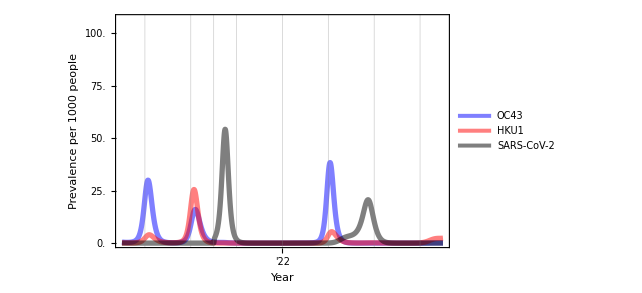

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3F.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3F.png",figinvasion];
```

### 70/0 | ∞ | w12:

#### Define parameter values:

```mathematica
chi31val=0.7;
chi32val = 0.7;
chi13val = 0;
chi23val = 0;
sigma3val = 1/Infinity;
importtime3 = 52*22 + 12;
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

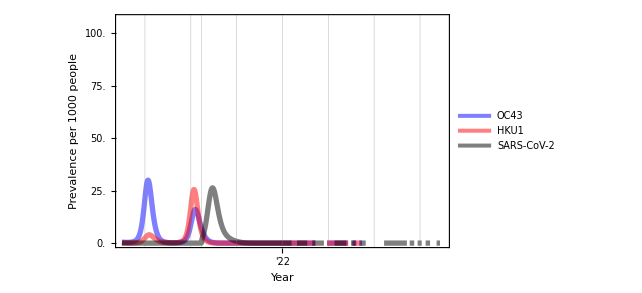

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3C.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3C.png",figinvasion];
```

### 30/0 | 40 | w12:

#### Define parameter values:

```mathematica
chi31val=0.3;
chi32val = 0.3;
chi13val = 0;
chi23val = 0;
sigma3val = 1/40;
importtime3 = 52*22 + 12;
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

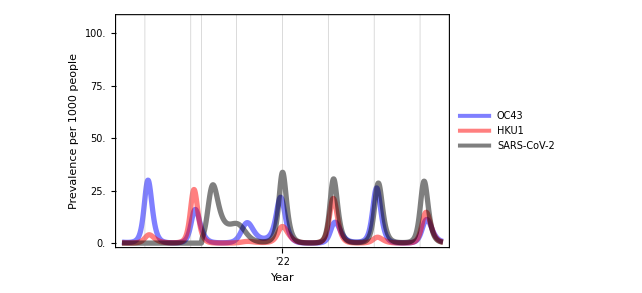

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3A.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3A.png",figinvasion];
```

### 30/0 | 40 | w36:

#### Define parameter values:

```mathematica
chi31val=0.3;
chi32val = 0.3;
chi13val = 0;
chi23val = 0;
sigma3val = 1/40;
importtime3 = 52*22 + 36;
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

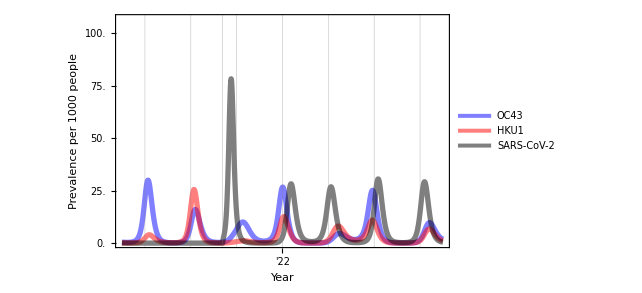

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3B.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3B.png",figinvasion];
```

### 30/30 | 104 | w32:

#### Define parameter values:

```mathematica
chi31val=0.3;
chi32val = 0.3;
chi13val = 0.3;
chi23val = 0.3;
sigma3val = 1/104;
importtime3 = 52*22 + 32;
```

#### Run the model:

```mathematica
sol=runmodel3strain[];
```

#### Plot output:

```mathematica
figinvasion = Plot[{Evaluate[{{100*scalingfactor*(I1S2S3[t]+I1S2E3[t]+I1S2I3[t]+I1S2R3[t]+I1E2S3[t]+I1E2E3[t]+I1E2I3[t]+I1E2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+I1R2S3[t]+I1R2E3[t]+I1R2I3[t]+I1R2R3[t])},{100*scalingfactor*(S1I2S3[t]+S1I2E3[t]+S1I2I3[t]+S1I2R3[t]+E1I2S3[t]+E1I2E3[t]+E1I2I3[t]+E1I2R3[t]+I1I2S3[t]+I1I2E3[t]+I1I2I3[t]+I1I2R3[t]+R1I2S3[t]+R1I2E3[t]+R1I2I3[t]+R1I2R3[t])},
{100*scalingfactor*(S1S2I3[t]+S1E2I3[t]+S1I2I3[t]+S1R2I3[t]+E1S2I3[t]+E1E2I3[t]+E1I2I3[t]+E1R2I3[t]+I1S2I3[t]+I1E2I3[t]+I1I2I3[t]+I1R2I3[t]+R1S2I3[t]+R1E2I3[t]+R1I2I3[t]+R1R2I3[t])}}/.sol]},Join[{t},plotwindow],PlotRange->{0, plotrangemax}, 
GridLines -> {Join[Table[{i, yearbarchar}, {i, 0, tmax, 52}],{{importtime3,importbarchar}}],None},
Frame->{True,True,False,True}, PlotRangePadding->None, BaseStyle->FontSize->fs, 
FrameTicks-> {{ncovticks, All},{Table[{i, "'"<>ToString[i/52-2]}, {i,0,tmax,52}], Automatic}},
FrameLabel->{"Year","Prevalence per 1000 people", Automatic, "%Positive × %ILI"}, ImageSize->imsz, PlotLegends->{"OC43","HKU1","SARS-CoV-2"}, PlotStyle->{oc43char, hku1char,ncovchar}];
```

#### Save output:

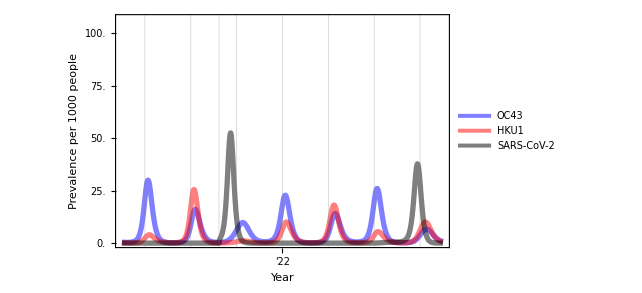

```mathematica
figinvasion
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3D.pdf",figinvasion];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig3D.png",figinvasion];
```

# Single-strain model with interventions

## Set parameter values and define functions:

```mathematica
(*Seasonal forcing*)
beta[t_,amplitude_,baseline_,phival_,gammaval_]:=gammaval*(amplitude/2*Cos[2*Pi*(t-phival)/52]+(amplitude/2+baseline))

pC = (0.3)*(0.044); (*Probability of needing critical care*)
pH = (0.7)*(0.044); (*Probability of hospitalization but not critical care*)
pS = 1-(pC + pH); (*Probability of not needing care*)

nuval = 1/(4.9/7); (*Rate of progressing to infectiousness*)
gammaval = 1/(4.8/7); (*Rate of losing infectiousness or going to the hospital*)

deltaHval = 1/(8/7); (*Rate of leaving hospital for those not going to critical care*)
deltaCval = 1/(6/7); (*Rate of leaving hospital and going to critical care*)
xiCval = 1/(10/7); (*Rate of leaving critical care*)
 
amplitude = 0.6; 
baseline = 1.4; 
phival= -3.8;

kappaval = 0.01;
importtime = (31+29+11)/7; 
importlength = 0.5;

ptest = 0.05; (*probability that a non-hospitalized case gets tested*)

tmax = 5*52;

plotwindow = {0, 64};
plotwindowlong = {0, 52*2.5};
fs = 18;
imsz=400;
seasonality = 1;

thresholdprevon = 0.0035; (*0.00375;*)
thresholdprevoff = 0.001; (*0.001;*)

thresholdprevonmoreICU = 0.007; (*0.0075*)
thresholdprevoffmoreICU = 0.002; (*0.00025*)
```

## One-time intervention model

```mathematica
runmodeloneshot[] := NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t] == 0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[t>npistart, npi[t]->1-npifactor],
WhenEvent[t>npiend, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

## Scenarios without seasonality:

### No reduction in transmission:

```mathematica
npifactor = 0.0;
npistart = Infinity;
npiend = Infinity;
seasonality=0;
solns=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=0;
sol20x2x4ns=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=0;
sol40x2x4ns=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=0;
sol60x2x4ns=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=0;
sol20x2x8ns=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=0;
sol40x2x8ns=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=0;
sol60x2x8ns=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=0;
sol20x2x12ns=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=0;
sol40x2x12ns=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=0;
sol60x2x12ns=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=0;
sol20x2x20ns=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=0;
sol40x2x20ns=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=0;
sol60x2x20ns=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, always on, w/out seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=0;
sol20x2xinfns=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, always on, w/out seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=0;
sol40x2xinfns=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, always on, w/out seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=0;
sol60x2xinfns=runmodeloneshot[];
```

## Scenarios with seasonality:

### No reduction in transmission:

```mathematica
npifactor = 0.0;
npistart = Infinity;
npiend = Infinity;
seasonality=1;
sols=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=1;
sol20x2x4s=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=1;
sol40x2x4s=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 4 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 4;
seasonality=1;
sol60x2x4s=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=1;
sol20x2x8s=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=1;
sol40x2x8s=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 8 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 8;
seasonality=1;
sol60x2x8s=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=1;
sol20x2x12s=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=1;
sol40x2x12s=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 12 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 12;
seasonality=1;
sol60x2x12s=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=1;
sol20x2x20s=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=1;
sol40x2x20s=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, for 20 weeks, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + 20;
seasonality=1;
sol60x2x20s=runmodeloneshot[];
```

### 20% reduction in transmission, 2 weeks after establishment, always on, w/seasonality:

```mathematica
npifactor = 0.2;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=1;
sol20x2xinfs=runmodeloneshot[];
```

### 40% reduction in transmission, 2 weeks after establishment, always on, w/seasonality:

```mathematica
npifactor = 0.4;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=1;
sol40x2xinfs=runmodeloneshot[];
```

### 60% reduction in transmission, 2 weeks after establishment, always on, w/seasonality:

```mathematica
npifactor = 0.6;
npistart = importtime + 2;
npiend = npistart + Infinity;
seasonality=1;
sol60x2xinfs=runmodeloneshot[];
```

## Scenarios without seasonality, with brake-pumping, prevalence-based threshold

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
seasonality=0;
sol60bpnsprev=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevon, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoff, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

## Scenarios with seasonality, with brake-pumping, prevalence-based threshold

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
seasonality=1;
sol60bpsprev=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevon, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoff, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est, npi},{t, 0, tmax}
];
```

## Scenarios without seasonality, with brake-pumping, prevalence-based threshold, and a higher threshold assuming more ICU beds:

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
seasonality=0;
sol60bpnsprevmoreICU=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevonmoreICU, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoffmoreICU, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est,npi},{t, 0, tmax}
];
```

## Scenarios without seasonality, with brake-pumping, prevalence-based threshold, and a higher threshold assuming more ICU beds:

### 60% reduction in transmission:

```mathematica
npifactor = 0.6;
seasonality=1;
sol60bpsprevmoreICU=NDSolve[{
Sq'[t] == -npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] - est[t]*Sq[t],
Eq'[t] == npi[t]*beta[t, seasonality*amplitude, baseline+(1-seasonality)*amplitude, phival, gammaval]*(ISq[t] + IHq[t] + ICq[t])*Sq[t] + est[t]*Sq[t] - (pS + pH + pC)*nuval*Eq[t],
ISq'[t] == pS*nuval*Eq[t] - gammaval*ISq[t],
RSq'[t] == gammaval*ISq[t],
IHq'[t] == pH*nuval*Eq[t] - gammaval*IHq[t],
HHq'[t]== gammaval*IHq[t] - deltaHval*HHq[t], 
RHq'[t] == deltaHval*HHq[t],
ICq'[t] == pC*nuval*Eq[t] - gammaval*ICq[t],
HCq'[t] == gammaval*ICq[t] - deltaCval*HCq[t],
CCq'[t] ==deltaCval*HCq[t] - xiCval*CCq[t],
RCq'[t] == xiCval*CCq[t],
est'[t]==0,
npi'[t]==0,
WhenEvent[t≥importtime , est[t]->kappaval], 
WhenEvent[t >importtime+importlength, est[t]->0 ],
WhenEvent[ISq[t] + IHq[t] + ICq[t]>thresholdprevonmoreICU, npi[t]->1-npifactor],
WhenEvent[ISq[t] + IHq[t] + ICq[t]<thresholdprevoffmoreICU, npi[t]->1],
Sq[0] ==1, Eq[0]==0,ISq[0]==0,RSq[0]==0,IHq[0]==0,HHq[0]==0,RHq[0]==0,ICq[0]==0,HCq[0]==0,CCq[0]==0,RCq[0]==0,est[0]==0, npi[0]==1
},{Sq, Eq, ISq, RSq, IHq, HHq, RHq, ICq, HCq, CCq, RCq, est,npi},{t, 0, tmax}
];
```

## Plot incidence without seasonality for one-time interventions (Figure 4):

```mathematica
line1char = {Black};
line2char = {Red};
line3char = {Blue};
line4char = {Green};

line5char = {Black, Dashed};
line6char = {Red, Dashed};
line7char = {Blue, Dashed};
line8char = {Green, Dashed};

prmax = 850;
```

### Four weeks:

```mathematica
sf = 40;
```

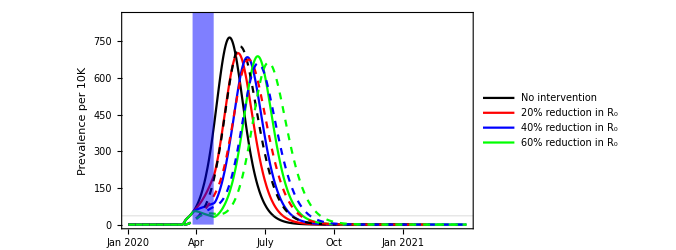

```mathematica
figoneshot4nscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x4ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x4ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x4ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x4ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x4ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x4ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[N[1/sf*#]]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+4,2000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4A.pdf",figoneshot4nscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4A.png",figoneshot4nscrit];
```

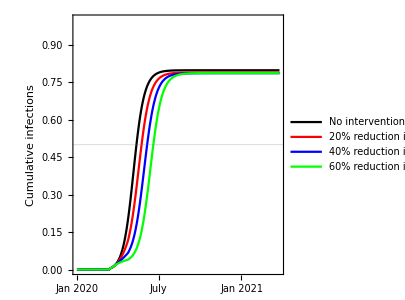

```mathematica
figoneshot4nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x4ns],
Evaluate[1-Sq[t]/.sol40x2x4ns],
Evaluate[1-Sq[t]/.sol60x2x4ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4F.pdf",figoneshot4nscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4F.png",figoneshot4nscritcumS];
```

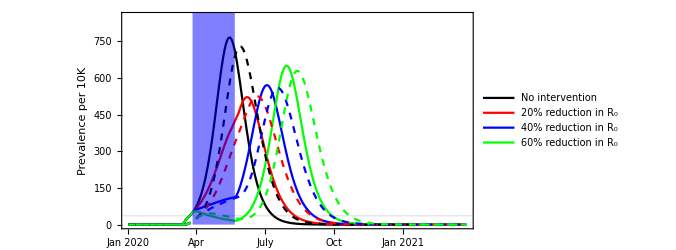

```mathematica
figoneshot8nscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x8ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x8ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x8ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x8ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x8ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x8ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+8,2000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4B.pdf",figoneshot8nscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4B.png",figoneshot8nscrit];
```

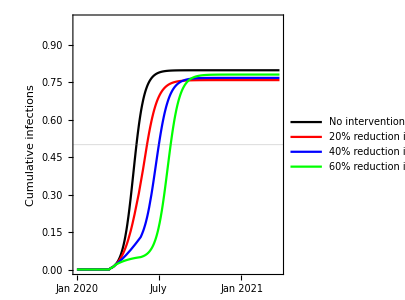

```mathematica
figoneshot8nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x8ns],
Evaluate[1-Sq[t]/.sol40x2x8ns],
Evaluate[1-Sq[t]/.sol60x2x8ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4G.pdf",figoneshot8nscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4G.png",figoneshot8nscritcumS];
```

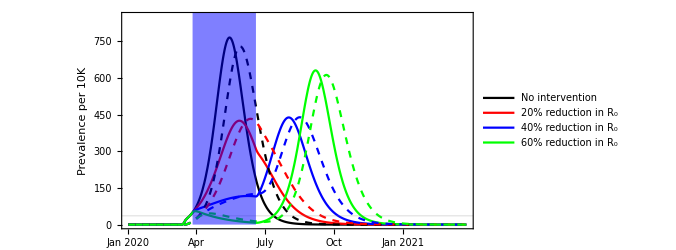

```mathematica
figoneshot12nscrit =Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x12ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x12ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x12ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x12ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x12ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x12ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+12,2000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4C.pdf",figoneshot12nscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4C.png",figoneshot12nscrit];
```

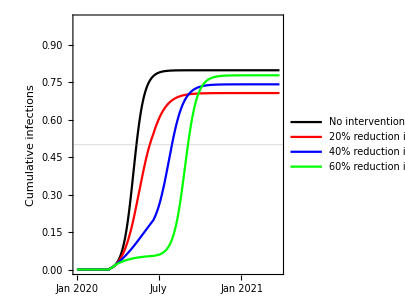

```mathematica
figoneshot12nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x12ns],
Evaluate[1-Sq[t]/.sol40x2x12ns],
Evaluate[1-Sq[t]/.sol60x2x12ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4H.pdf",figoneshot12nscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4H.png",figoneshot12nscritcumS];
```

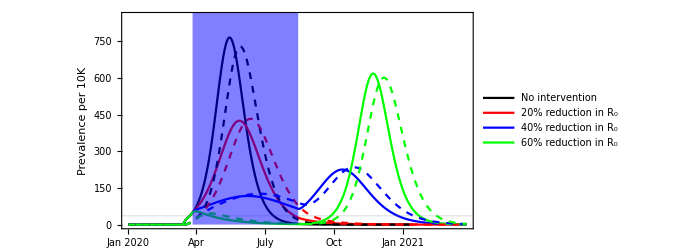

```mathematica
figoneshot20nscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x20ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x20ns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x20ns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2x20ns],
sf * 10000*Evaluate[CCq[t]/.sol40x2x20ns],
sf * 10000*Evaluate[CCq[t]/.sol60x2x20ns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+20,2000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4D.pdf",figoneshot20nscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4D.png",figoneshot20nscrit];
```

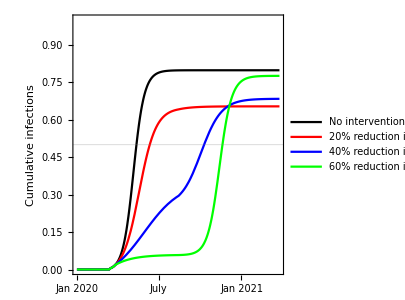

```mathematica
figoneshot20nscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2x20ns],
Evaluate[1-Sq[t]/.sol40x2x20ns],
Evaluate[1-Sq[t]/.sol60x2x20ns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4I.pdf",figoneshot20nscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4I.png",figoneshot20nscritcumS];
```

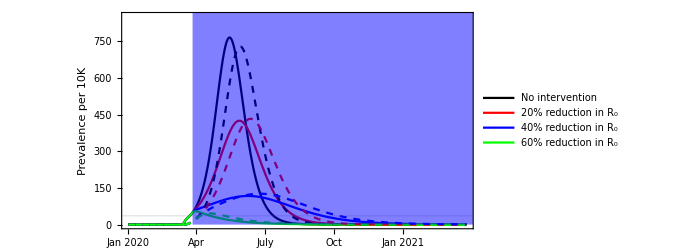

```mathematica
figoneshotinfnscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.solns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2xinfns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2xinfns],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2xinfns], 
sf * 10000*Evaluate[CCq[t]/.solns],
sf * 10000*Evaluate[CCq[t]/.sol20x2xinfns],
sf * 10000*Evaluate[CCq[t]/.sol40x2xinfns],
sf * 10000*Evaluate[CCq[t]/.sol60x2xinfns]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+10000,2000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4E.pdf",figoneshotinfnscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4E.png",figoneshotinfnscrit];
```

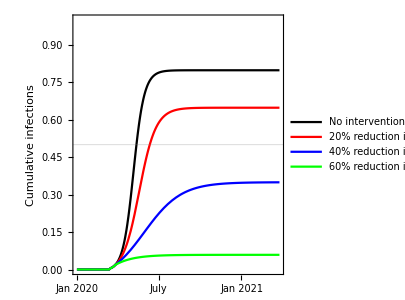

```mathematica
figoneshotinfnscritcumS = Plot[{
Evaluate[1-Sq[t]/.solns],
Evaluate[1-Sq[t]/.sol20x2xinfns],
Evaluate[1-Sq[t]/.sol40x2xinfns],
Evaluate[1-Sq[t]/.sol60x2xinfns],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4J.pdf",figoneshotinfnscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig4J.png",figoneshotinfnscritcumS];
```

## Plot incidence with seasonality for one-time interventions (Figure 5):

### Plot characteristics:

```mathematica
line1char = {Black};
line2char = {Red};
line3char = {Blue};
line4char = {Green};

line5char = {Black, Dashed};
line6char = {Red, Dashed};
line7char = {Blue, Dashed};
line8char = {Green, Dashed};

prmax = 800; (*800*)
```

### Four weeks:

```mathematica
sf = 40;
```

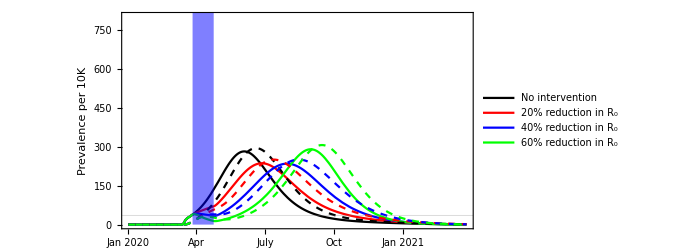

```mathematica
figoneshot4scrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x4s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x4s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x4s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x4s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x4s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x4s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+4,1000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5A.pdf",figoneshot4scrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5A.png",figoneshot4scrit];
```

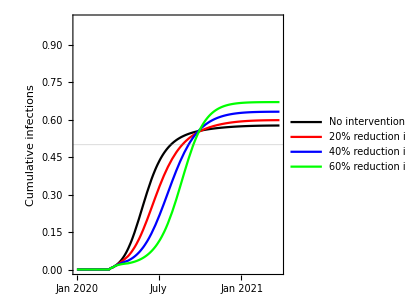

```mathematica
figoneshot4scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x4s],
Evaluate[1-Sq[t]/.sol40x2x4s],
Evaluate[1-Sq[t]/.sol60x2x4s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5F.pdf",figoneshot4scritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5F.png",figoneshot4scritcumS];
```

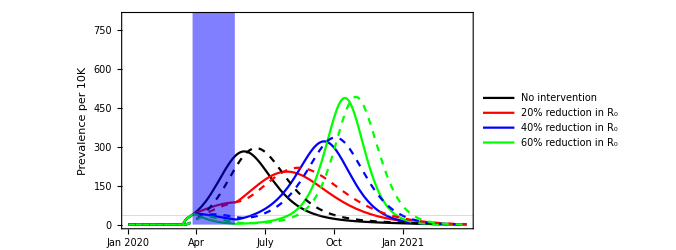

```mathematica
figoneshot8scrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x8s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x8s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x8s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x8s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x8s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x8s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+8,1000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5B.pdf",figoneshot8scrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5B.png",figoneshot8scrit];
```

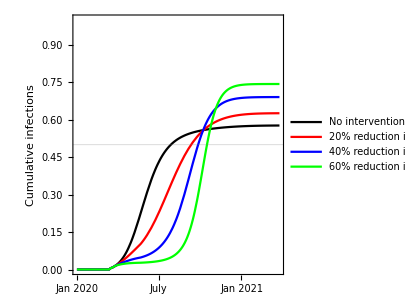

```mathematica
figoneshot8scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x8s],
Evaluate[1-Sq[t]/.sol40x2x8s],
Evaluate[1-Sq[t]/.sol60x2x8s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5G.pdf",figoneshot8scritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5G.png",figoneshot8scritcumS];
```

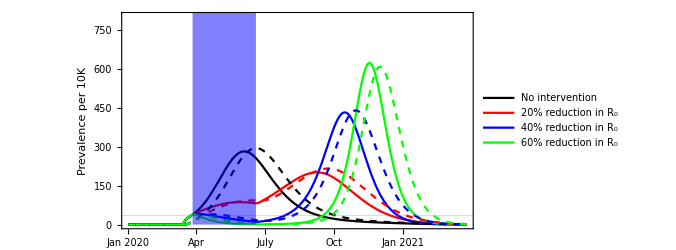

```mathematica
figoneshot12scrit =Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x12s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x12s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x12s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x12s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x12s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x12s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+12,1000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5C.pdf",figoneshot12scrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5C.png",figoneshot12scrit];
```

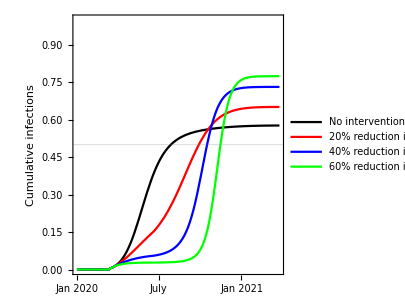

```mathematica
figoneshot12scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x12s],
Evaluate[1-Sq[t]/.sol40x2x12s],
Evaluate[1-Sq[t]/.sol60x2x12s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5H.pdf",figoneshot12scritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5H.png",figoneshot12scritcumS];
```

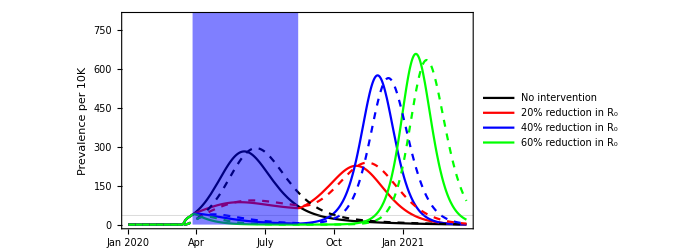

```mathematica
figoneshot20scrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2x20s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2x20s],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2x20s], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2x20s],
sf * 10000*Evaluate[CCq[t]/.sol40x2x20s],
sf * 10000*Evaluate[CCq[t]/.sol60x2x20s]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+20,1000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5D.pdf",figoneshot20scrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5D.png",figoneshot20scrit];
```

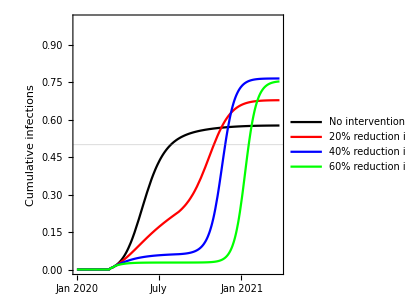

```mathematica
figoneshot20scritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2x20s],
Evaluate[1-Sq[t]/.sol40x2x20s],
Evaluate[1-Sq[t]/.sol60x2x20s],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5I.pdf",figoneshot20scritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5I.png",figoneshot20scritcumS];
```

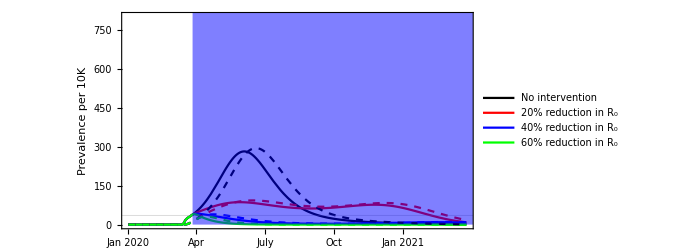

```mathematica
figoneshotinfscrit = Plot[{
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sols],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol20x2xinfs],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol40x2xinfs],
10000*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60x2xinfs], 
sf * 10000*Evaluate[CCq[t]/.sols],
sf * 10000*Evaluate[CCq[t]/.sol20x2xinfs],
sf * 10000*Evaluate[CCq[t]/.sol40x2xinfs],
sf * 10000*Evaluate[CCq[t]/.sol60x2xinfs]
},Join[{t},plotwindow], PlotRange->{0,prmax}, FrameTicks->{{Automatic,{#, ToString[1/sf*#]}&/@FindDivisions[{0, prmax},5]},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None,"Critical cases per 10K"}, ImageSize->500, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{sf*10000*0.000089, {Orange, Thick, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"},AspectRatio->0.5,
Epilog->{Blue,Opacity[.5],Rectangle[{importtime+2,0},{importtime+2+10000,1000}]}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5E.pdf",figoneshotinfscrit];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5E.png",figoneshotinfscrit];
```

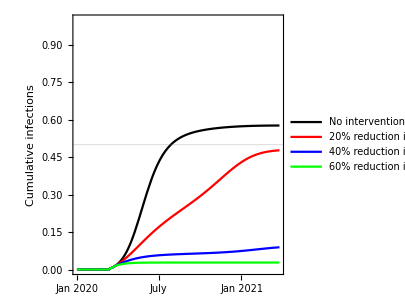

```mathematica
figoneshotinfscritcumS = Plot[{
Evaluate[1-Sq[t]/.sols],
Evaluate[1-Sq[t]/.sol20x2xinfs],
Evaluate[1-Sq[t]/.sol40x2xinfs],
Evaluate[1-Sq[t]/.sol60x2xinfs],
},Join[{t},plotwindow], PlotRange->{0,1}, FrameTicks->{{Automatic,None},{{
{0, "Jan\n2020"},
{(31+28+31)/7, "Apr"}, 
{(31+28+31+30+31+30)/7, "July"}, 
{(31+28+31+30+31+30+31+31+30)/7, "Oct"},
{52, "Jan\n2021"}}, Automatic}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Cumulative infections"}, ImageSize->300, PlotStyle->{line1char, line2char, line3char, line4char, line5char, line6char, line7char, line8char},GridLines->{{},{{1-1/(amplitude+baseline),{Black, Opacity[1]}}}},
PlotLegends->{"No intervention", "20% reduction in R_0","40% reduction in R_0", "60% reduction in R_0"}, AspectRatio->1]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5J.pdf",figoneshotinfscritcumS];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig5J.png",figoneshotinfscritcumS];
```

## Define key variables for the brakepump strategies:

```mathematica
dateticks = {
{0, Rotate["Jan",π/2]},
{0, Text[Style["\n\n2020", FontSize->14]]},
{(31)/7,""},
{(31+28)/7,""},
{(31+28+31)/7, Rotate["Apr",π/2]}, 
{(31+28+31+30)/7,""}, 
{(31+28+31+30+31)/7,""}, 
{(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{(31+28+31+30+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31)/7, ""},
{(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]},
{(31+28+31+30+31+30+31+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31+30+31+30)/7, ""},
{52, Rotate["Jan",π/2]},
{52, Text[Style["\n\n2021", FontSize->14]]},
{52+(31)/7,""}, 
{52+(31+28)/7, ""}, 
{52+(31+28+31)/7, Rotate["Apr",π/2]}, 
{52+(31+28+31+30)/7, ""}, 
{52+(31+28+31+30+31)/7, ""}, 
{52+(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{52+(31+28+31+30+31+30+31)/7, ""},
{52+(31+28+31+30+31+30+31+31)/7, ""},
{52+(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]},
{52+(31+28+31+30+31+30+31+31+30+31)/7,""},
{52+(31+28+31+30+31+30+31+31+30+31+30)/7,""},
{52*2, Rotate["Jan",π/2]}, 
{52*2, Text[Style["\n\n2022", FontSize->14]]}, 
{52*2+(31)/7, ""}, 
{52*2+(31+28)/7, ""}, 
{52*2+(31+28+31)/7, Rotate["Apr",π/2]}, 
{52*2+(31+28+31+30)/7,""}, 
{52*2+(31+28+31+30+31)/7,""}, 
{52*2+(31+28+31+30+31+30)/7, Rotate["July",π/2]}, 
{52*2+(31+28+31+30+31+30+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31+30)/7, Rotate["Oct",π/2]}};
```

```mathematica
yearticks = {
{0, Rotate["2020",π/2]},
{(31)/7,""},
{(31+28)/7,""},
{(31+28+31)/7, ""}, 
{(31+28+31+30)/7,""}, 
{(31+28+31+30+31)/7,""}, 
{(31+28+31+30+31+30)/7,""}, 
{(31+28+31+30+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31)/7, ""},
{(31+28+31+30+31+30+31+31+30)/7, ""},
{(31+28+31+30+31+30+31+31+30+31)/7,""},
{(31+28+31+30+31+30+31+31+30+31+30)/7, ""},
{52, Rotate["2021",π/2]},
{52+(31)/7,""}, 
{52+(31+28)/7, ""}, 
{52+(31+28+31)/7,""}, 
{52+(31+28+31+30)/7, ""}, 
{52+(31+28+31+30+31)/7, ""}, 
{52+(31+28+31+30+31+30)/7,""}, 
{52+(31+28+31+30+31+30+31)/7, ""},
{52+(31+28+31+30+31+30+31+31)/7, ""},
{52+(31+28+31+30+31+30+31+31+30)/7, ""},
{52+(31+28+31+30+31+30+31+31+30+31)/7,""},
{52+(31+28+31+30+31+30+31+31+30+31+30)/7,""},
{52*2, Rotate["2022",π/2]}, 
{52*2+(31)/7, ""}, 
{52*2+(31+28)/7, ""}, 
{52*2+(31+28+31)/7,""}, 
{52*2+(31+28+31+30)/7,""}, 
{52*2+(31+28+31+30+31)/7,""}, 
{52*2+(31+28+31+30+31+30)/7, ""}, 
{52*2+(31+28+31+30+31+30+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31)/7, ""},
{52*2+(31+28+31+30+31+30+31+31+30)/7, ""}};
```

```mathematica
ar = 0.25;
```

```mathematica
imsz=700;
```

## Plot the continued rise in ICU cases after implementation of distancing, with prevalence, no seasonality:

```mathematica
sf = 0.02;
prmax = 1;
```

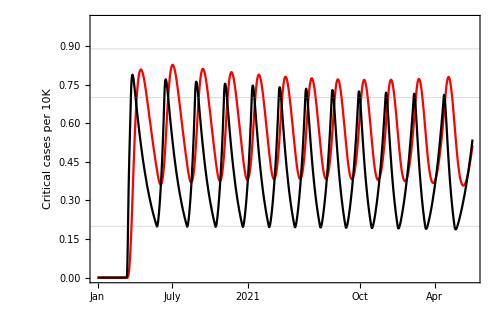

```mathematica
figcritprevbp = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5]},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Critical cases per 10K",None, "Prevalence per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

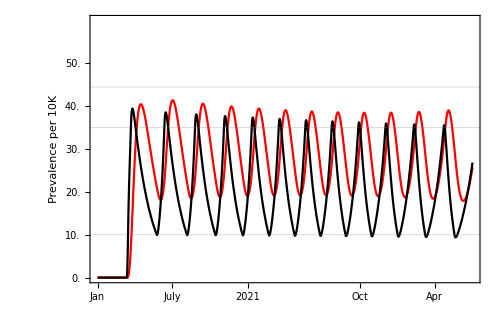

```mathematica
figcritprevbp = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1.2}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0,1},5],All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibp = Plot[10*Evaluate[1-npi[t]/.sol60bpnsprev],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

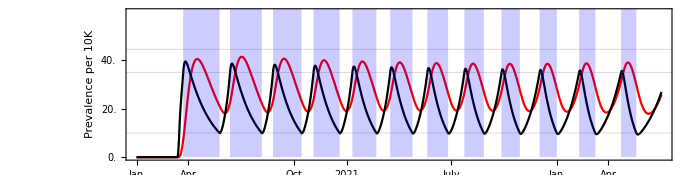

```mathematica
figcritprevbpnpi = Show[{figcritprevbp, fignpibp}, PlotRange->PlotRange[figcritprevbp], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6A.pdf",figcritprevbpnpi];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6A.png",figcritprevbpnpi];
```

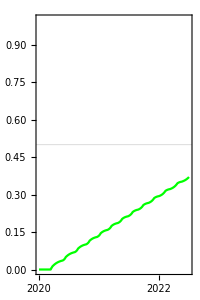

```mathematica
figcritprevbpnpiimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpnsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"},PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}, ImageSize-> 200]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6E.pdf",figcritprevbpnpiimm];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6E.png",figcritprevbpnpiimm];
```

## Plot the continued rise in ICU cases after implementation of distancing, with prevalence, with seasonality:

```mathematica
sf = 0.02;
prmax = 1;
```

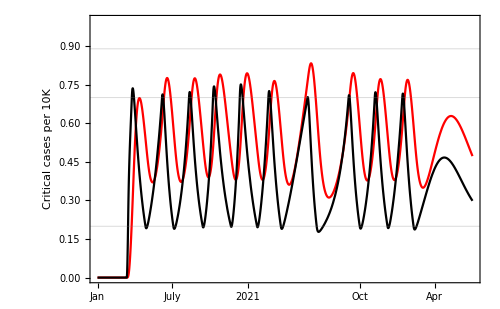

```mathematica
figcritprevbps = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5]},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Critical cases per 10K",None, "Prevalence per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

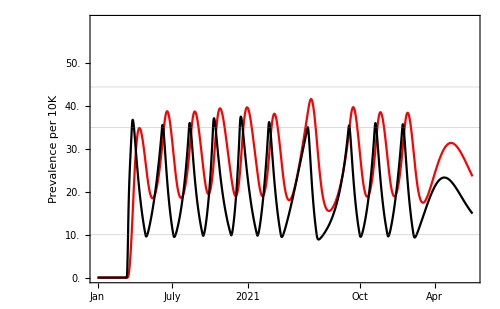

```mathematica
figcritprevbps = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprev],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1.2}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089,{Black, Opacity[1]}}, {10000*sf*thresholdprevon, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoff, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibps = Plot[10*Evaluate[1-npi[t]/.sol60bpsprev],{t,0,130}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

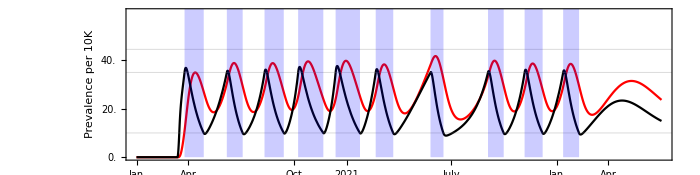

```mathematica
figcritprevbpsnpi = Show[{figcritprevbps, fignpibps}, PlotRange->PlotRange[figcritprevbps], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6B.pdf",figcritprevbpsnpi];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6B.png",figcritprevbpsnpi];
```

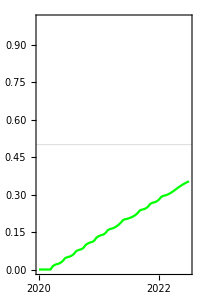

```mathematica
figcritprevbpsnpiimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpsprev]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6F.pdf",figcritprevbpsnpiimm];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6F.png",figcritprevbpsnpiimm];
```

## Plot the continued rise in ICU cases after implementation of distancing, with prevalence, without seasonality, and double the ICU capacity:

```mathematica
sf = 0.02;
prmax = 2;
```

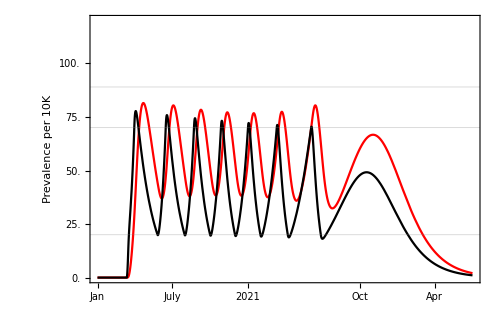

```mathematica
figcritprevbpnsmoreICU = Plot[{
10000*Evaluate[CCq[t]/.sol60bpnsprevmoreICU],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpnsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 2.4}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089*2,{Black, Opacity[1]}},  {10000*sf*thresholdprevonmoreICU, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoffmoreICU, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibpnsmoreICU = Plot[10*Evaluate[1-npi[t]/.sol60bpnsprevmoreICU],{t,0,100}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

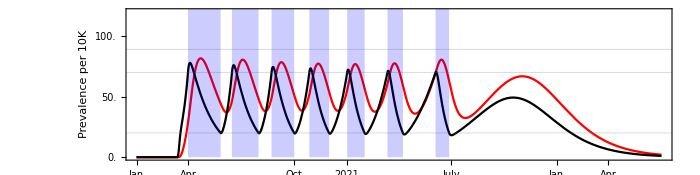

```mathematica
figcritprevbpnsnpimoreICU = Show[{figcritprevbpnsmoreICU, fignpibpnsmoreICU}, PlotRange->PlotRange[figcritprevbpnsmoreICU], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6C.pdf",figcritprevbpnsnpimoreICU];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6C.png",figcritprevbpnsnpimoreICU];
```

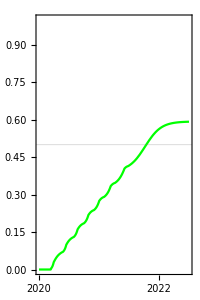

```mathematica
figcritprevbpnsnpimoreICUimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpnsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{ },{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6G.pdf",figcritprevbpnsnpimoreICUimm];Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6G.png",figcritprevbpnsnpimoreICUimm];
```

## Plot the continued rise in ICU cases after implementation of distancing, with prevalence, with seasonality, and double the ICU capacity:

```mathematica
sf = 0.02;
prmax = 2;
```

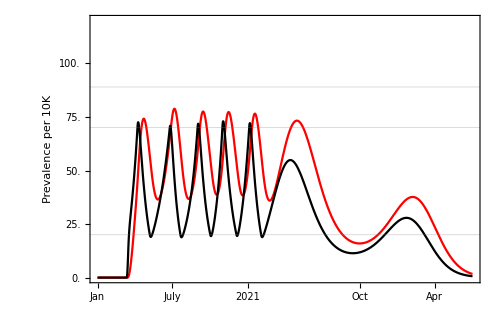

```mathematica
figcritprevbpsmoreICU = Plot[{
10000*Evaluate[CCq[t]/.sol60bpsprevmoreICU],
10000*sf*Evaluate[ISq[t]+IHq[t] + ICq[t]/.sol60bpsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 2.4}, FrameTicks->{{{#, ToString[(1/sf)*#]}&/@FindDivisions[{0, prmax},5], All},{dateticks, Automatic}}, Frame->{True,True,False,True}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->fs, FrameLabel->{None,"Prevalence per 10K",None, "Critical cases per 10K"}, ImageSize->500, PlotStyle->{Red, Black},GridLines->{{},{{10000*.000089*2,{Black, Opacity[1]}},  {10000*sf*thresholdprevonmoreICU, {Black, Dashed, Opacity[1]}}, {10000*sf*thresholdprevoffmoreICU, {Black, Dashed, Opacity[1]}}}}]
```

```mathematica
fignpibpsmoreICU = Plot[10*Evaluate[1-npi[t]/.sol60bpsprevmoreICU],{t,0,100}, Filling->Axis, PlotStyle->{Blue, Opacity[0]}];
```

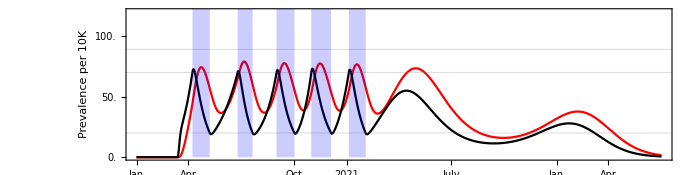

```mathematica
figcritprevbpsnpimoreICU = Show[{figcritprevbpsmoreICU, fignpibpsmoreICU}, PlotRange->PlotRange[figcritprevbpsmoreICU], AspectRatio->ar, ImageSize->imsz]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6D.pdf",figcritprevbpsnpimoreICU];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6D.png",figcritprevbpsnpimoreICU];
```

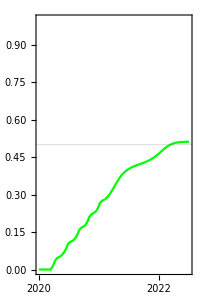

```mathematica
figcritprevbpsnpimoreICUimm = Plot[{
Evaluate[1-Sq[t]/.sol60bpsprevmoreICU]
},Join[{t},plotwindowlong], PlotRange->{0, 1}, FrameTicks->{{Automatic,None},{yearticks, None}}, Frame->{True,True,False,False}, PlotRangePadding->{Automatic,None},BaseStyle->FontSize->22, FrameLabel->{None,"Cumulative infections"}, ImageSize->200, PlotStyle->Green, AspectRatio->1.5, GridLines->{{},{{1-1/(baseline+amplitude),{Black, Opacity[1]}}}}]
```

```mathematica
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6H.pdf",figcritprevbpsnpimoreICUimm];
Export["/Users/sk792/DropboxHarvard/Projects/Wuhan/writeup/Science/Submission2/figures/fig6H.png",figcritprevbpsnpimoreICUimm];
```